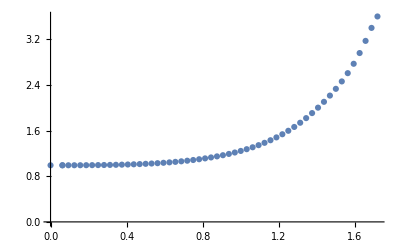

```mathematica
c={{0,4.289559},{0.062500,4.264998},{0.062500,4.264998},{0.093750,4.251975},{0.125000,4.238299},{0.156250,4.223933},{0.187500,4.208871},{0.218750,4.193132},{0.250000,4.176751},{0.281250,4.159781},{0.312500,4.142287},{0.343750,4.124348},{0.375000,4.106052},{0.406250,4.087502},{0.437500,4.068810},{0.468750,4.050102},{0.500000,4.031517},{0.531250,4.013207},{0.562500,3.995339},{0.593750,3.978095},{0.625000,3.961677},{0.656250,3.946302},{0.687500,3.932210},{0.718750,3.919663},{0.750000,3.908946},{0.781250,3.900373},{0.812500,3.894287},{0.843750,3.891062},{0.875000,3.891111},{0.906250,3.894883},{0.937500,3.902875},{0.968750,3.915630},{1.000000,3.933746},{1.031250,3.957880},{1.062500,3.988755},{1.093750,4.027167},{1.125000,4.073993},{1.156250,4.130194},{1.187500,4.196823},{1.218750,4.275028},{1.250000,4.366043},{1.281250,4.471173},{1.312500,4.591749},{1.343750,4.729037},{1.375000,4.884112},{1.406250,5.057765},{1.437500,5.250736},{1.468750,5.464322},{1.500000,5.700691},{1.531250,5.962839},{1.562500,6.254618},{1.593750,6.580712},{1.625000,6.945955},{1.656250,7.352624},{1.687500,7.792152},{1.718750,8.224919}};
cc={{0,3.297434},{0.062500,3.272717},{0.062500,3.272717},{0.093750,3.259492},{0.125000,3.245502},{0.156250,3.230681},{0.187500,3.214996},{0.218750,3.198433},{0.250000,3.180992},{0.281250,3.162687},{0.312500,3.143545},{0.343750,3.123598},{0.375000,3.102892},{0.406250,3.081479},{0.437500,3.059421},{0.468750,3.036791},{0.500000,3.013669},{0.531250,2.990146},{0.562500,2.966324},{0.593750,2.942315},{0.625000,2.918243},{0.656250,2.894246},{0.687500,2.870472},{0.718750,2.847087},{0.750000,2.824270},{0.781250,2.802218},{0.812500,2.781145},{0.843750,2.761287},{0.875000,2.742899},{0.906250,2.726260},{0.937500,2.711675},{0.968750,2.699476},{1.000000,2.690025},{1.031250,2.683717},{1.062500,2.680983},{1.093750,2.682292},{1.125000,2.688156},{1.156250,2.699132},{1.187500,2.715828},{1.218750,2.738905},{1.250000,2.769078},{1.281250,2.807122},{1.312500,2.853871},{1.343750,2.910217},{1.375000,2.977093},{1.406250,3.055462},{1.437500,3.146269},{1.468750,3.250373},{1.500000,3.368444},{1.531250,3.500865},{1.562500,3.647783},{1.593750,3.809443},{1.625000,3.986517},{1.656250,4.180167},{1.687500,4.392049},{1.718750,4.624350}};
C1=c-cc*Table[{0,1},{i,0,55}];
ListPlot[C1]
```

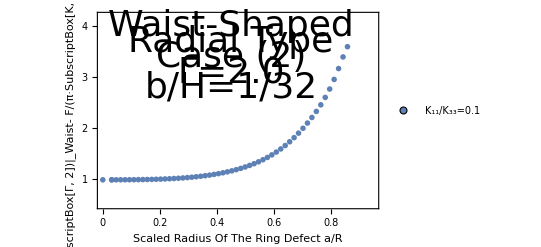

```mathematica
CC1=C1*Table[{0.5,1},{i,0,55}];
ListPlot[{CC1},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{1,2,3,4},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.95},{0.5,4.2}},FrameLabel->{{"F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Waist- F/(π·SubscriptBox[K, 33] H SuperscriptBox[Γ, 2])|_Cylinder", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1"},LegendMarkers->{{Graphics[Disk[]],12}}],{Right, Bottom}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.45,4.0}],Text[Style["Radial Type",Directive[Black,36]],{0.45,3.7}],Text[Style["Case (2)",Directive[Black,36]],{0.45,3.4}],Text[Style["Γ=2.0",Directive[Black,36]],{0.45,3.1}],Text[Style["b/H=1/32",Directive[Black,36]],{0.45,2.8}]}]
```